```mathematica
inf["neuralNetExplorations`"]
```

```mathematica
hp=64;
net=NetChain[
{
LinearLayer[hp],
BatchNormalizationLayer[],
Ramp,

LinearLayer[hp],
BatchNormalizationLayer[],
Ramp,

LinearLayer[1]
},"Input"->"Scalar","Output"->"Scalar"
]//NetInitialize;
```

```mathematica
weights[net]//Length
```

4865

```mathematica
NetGraph[net]
```

NetGraph[<>]

```mathematica
plotData[points_,color_]:=ListPlot[points,PlotStyle->Directive[color,PointSize[.01]],FrameTicks->False,PlotRangePadding->0.1,PlotRange->All];
```

```mathematica
plot=plotData[List@@@datum,GrayLevel[0.7]];
plotSolution[net_,t_]:=Show[plot,plotData[Transpose[{Range[-20,30,.02],net@Range[-20,30,.02]}],Magenta],Epilog->Text[t,{10,0.9},{-1,0}]]
```

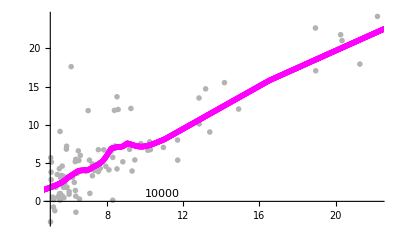
-Graphics-
{{1.87101×10^-8,-3.41514×10^-9,-6.37307×10^-8,-1.98573×10^-8,7.59113×10^-10,-6.16902×10^-9,1.28476×10^-7,1.039×10^-9,8.72032×10^-7,6.71912×10^-7,-3.89158×10^-8,-1.68333×10^-8,1.26626×10^-7,2.44986×10^-8,2.1271×10^-8,-1.3247×10^-8,-6.78463×10^-9,3.17792×10^-8,-3.22619×10^-8,3.04103×10^-8,1.04758×10^-8,-5.27708×10^-8,2.23139×10^-9,-4.38199×10^-8,1.14224×10^-7,-5.09018×10^-8,5.95669×10^-9,9.96105×10^-8,-4.62744×10^-8,2.05082×10^-8,-1.07111×10^-7,-2.65607×10^-9,-7.53338×10^-8,-4.86817×10^-8,-9.09276×10^-8,1.23242×10^-8,1.08997×10^-8,-4.15849×10^-8,-6.02575×10^-8,3.37231×10^-8,-4.20362×10^-8,3.6493×10^-7,1.98131×10^-8,-7.28864×10^-8,3.22196×10^-8,-3.64042×10^-8,-1.27104×10^-7,3.75936×10^-9,-3.57086×10^-8,6.25471×10^-10,1.70969×10^-8,-1.37178×10^-8,6.11246×10^-9,3.44513×10^-8,3.50833×10^-8,3.99993×10^-9,-6.69286×10^-8,-3.27961×10^-8,-2.17274×10^-8,-4.66746×10^-8,4.33798×10^-8,8.0443×10^-9,-1.15271×10^-7,4.57979×10^-8,0.233631,0.147915,-0.159409,0.248864,-0.13595,-0.145325,0.157098,-0.0599327,0.120982,0.173753,-0.073436,-0.0620041,0.235751,0.19711,0.21781,-0.235779,0.301927,0.143486,0.14932,-0.145189,-0.206482,-0.129542,-0.28992,-0.139691,0.155156,-0.0481855,0.37825,0.245986,0.23975,0.0493947,0.618233,-0.2605,0.141249,-0.50317,-0.173429,0.232437,-0.0946959,0.139512,-0.143671,-0.170078,0.24975,0.0190354,-0.079779,-0.420034,0.216882,0.201658,-0.227172,-0.294845,0.122759,0.11532,-0.192793,-0.201658,0.102333,0.303885,0.268761,0.129583,0.162269,-0.054873,-0.0976859,-0.132537,0.232248,0.247327,0.125295,0.111187}}

```mathematica
trained=NetTrain[net,Rule@@@datum,
Method->{"SGD","LearningRate"->0.001},
TargetDevice->"CPU",
MaxTrainingRounds->Quantity[20,"Seconds"],TrainingProgressReporting->{Style[Grid[{{plotSolution[#Net,#AbsoluteBatch]},{{#WeightsVector}}}],ImageSizeMultipliers->{1, 1}]&,"Interval"->0.1}];
Style[Grid[{{plotSolution[trained,10000]},List@{NetExtract[trained,{1,"Biases"}]~Join~Flatten@NetExtract[trained,{1,"Weights"}]}}],ImageSizeMultipliers->{1, 1}]
```